Solution to general 4 state model with forward k rates and reverse r rates

```mathematica
ass={ koff>0 , km>0, kp>0, kon>0, c0<c1, c1>0, c0>0, b > 1};
```

```mathematica
sol = FullSimplify[Solve[{J,J,J,J,1}=={k1 p1 - r1 p2, k2 p2 - r2 p3, k3 p3 - r3 p4, k4 p4 - r4 p1, p1+p2+p3+p4}, {J, p1,p2,p3,p4}]]
```

{{J→(k1 k2 k3 k4-r1 r2 r3 r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4),p1→(k2 k3 k4+k3 k4 r1+r1 r2 (k4+r3))/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4),p2→(k1 k4 (k3+r2)+k1 r2 r3+r2 r3 r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4),p3→(k1 k2 (k4+r3)+(k2+r1) r3 r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4),p4→(k1 k2 k3+k2 k3 r4+r1 (k3+r2) r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4)}}

Our specific system has symmetry, concentration dependence of activator binding (c) and energy input (b) on edge from state 2->1. when b = 1 then the system obeys detailed balance by construction

```mathematica
symSol =FullSimplify[sol/.{k1-> kp, r1->  b km, k3-> km, r3-> kp, k2-> c kon, r2-> koff, k4-> koff, r4-> c kon}]
```

{{J→-((-1+b) c km koff kon kp)/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))),p1→(km koff (c kon+b (km+koff+kp)))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))),p2→(koff kp (km+koff+c kon+kp))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))),p3→(c kon kp (b km+koff+c kon+kp))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))),p4→(c km kon (b (km+koff)+c kon+kp))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))}}

We are treating state 3 as the productive state - i.e. the one in which transcription happens. Copied p3 from above solution

```mathematica
p3cb[c_] = (c kon kp (b km+koff+c kon+kp))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)));
FullSimplify[p3cb[c] /. {b -> 1}]
```

(c kon kp)/((koff+c kon) (km+kp))

```mathematica
(* b = 1 forces equilibrium *) 
p3c[c_] = (c kon kp)/((koff+c kon) (km+kp));
```

```mathematica
(* calculate fidelity ratios in/out of equilibrium *)
eqRatio = FullSimplify[p3c[c1] / p3c[c0]]
noneqRatio = FullSimplify[p3cb[c1] / p3cb[c0]]
```

(c1 (koff+c0 kon))/(c0 (koff+c1 kon))

(c1 (koff+c0 kon) (b km+koff+c1 kon+kp) (c0 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))/(c0 (koff+c1 kon) (b km+koff+c0 kon+kp) (c1 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))

```mathematica
(* noneq = eq * gamma * delta *)
noneqComponent = noneqRatio / eqRatio
gamma = (b km+koff+c1 kon+kp) / (b km+koff+c0 kon+kp)
delta = noneqComponent / gamma
```

((b km+koff+c1 kon+kp) (c0 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))/((b km+koff+c0 kon+kp) (c1 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))

(b km+koff+c1 kon+kp)/(b km+koff+c0 kon+kp)

(c0 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))/(c1 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))

```mathematica
(* limit as k+ -> 0 is interesting because it simplifies *)
noneqLim = FullSimplify[Limit[noneqComponent, {kp->0}]];
(* Find the optimal values of beta - those maximizing the fidelity ratio *)
bMaxLim = Solve[D[noneqLim, b] == 0, b];
bMaxLim = FullSimplify[bMaxLim, ass]
```

{{b→1+√(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff)))},{b→1-√(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff)))}}

```mathematica
(* figure out what fidelity looks like at the optimal beta values. *)
activatedRoot =1+√(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff)));
noneqLimAtRoot = FullSimplify[noneqLim /. {b -> activatedRoot}]
noneqRatioLimAtRoot = FullSimplify[noneqLimAtRoot*eqRatio]
FullSimplify[Limit[noneqRatioLimAtRoot, {km->0}]]
```

((km+koff+c1 kon+km √(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff)))) (c0 kon+(km+koff) (1+√(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff))))))/((km+koff+c0 kon+km √(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff)))) (c1 kon+(km+koff) (1+√(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff))))))

(c1 (koff+c0 kon) (km+koff+c1 kon+km √(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff)))) (c0 kon+(km+koff) (1+√(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff))))))/(c0 (koff+c1 kon) (km+koff+c0 kon+km √(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff)))) (c1 kon+(km+koff) (1+√(((km+koff+c0 kon) (km+koff+c1 kon))/(km (km+koff))))))

c1/c0

### Solve for Optimal Beta

```mathematica
bMaxFull = Solve[D[noneqRatio, b] == 0, b];
```

```mathematica
bMaxFull  = FullSimplify[bMaxFull]
```

```mathematica
bMaxG1 =1-(√((c0-c1)^2 km^2 (koff+c0 kon)^2 (km+kp) (km+koff+kp) (km+koff+c0 kon+kp) (km+koff+c1 kon+kp)))/((c0-c1) km^2 (koff+c0 kon) (km+koff+kp));
```

```mathematica
fidelityMax = Simplify[noneqRatio /. {b -> bMaxG1}]
```

(c1 (koff+c0 kon) (km+koff+c1 kon+kp-(√((c0-c1)^2 km^2 (koff+c0 kon)^2 (km+kp) (km+koff+kp) (km+koff+c0 kon+kp) (km+koff+c1 kon+kp)))/((c0-c1) km (koff+c0 kon) (km+koff+kp))) (c0 kon (km+kp)+kp (km+koff+kp)+km (km+koff+kp) (1-(√((c0-c1)^2 km^2 (koff+c0 kon)^2 (km+kp) (km+koff+kp) (km+koff+c0 kon+kp) (km+koff+c1 kon+kp)))/((c0-c1) km^2 (koff+c0 kon) (km+koff+kp)))))/(c0 (koff+c1 kon) (km+koff+c0 kon+kp-(√((c0-c1)^2 km^2 (koff+c0 kon)^2 (km+kp) (km+koff+kp) (km+koff+c0 kon+kp) (km+koff+c1 kon+kp)))/((c0-c1) km (koff+c0 kon) (km+koff+kp))) (c1 kon (km+kp)+kp (km+koff+kp)+km (km+koff+kp) (1-(√((c0-c1)^2 km^2 (koff+c0 kon)^2 (km+kp) (km+koff+kp) (km+koff+c0 kon+kp) (km+koff+c1 kon+kp)))/((c0-c1) km^2 (koff+c0 kon) (km+koff+kp)))))

### Conduct Parameter Search (c1 = 10, c0 = kon = koff = 1)

```mathematica
fidelityMax1 = FullSimplify[fidelityMax /. {c0 -> 1, c1 -> 10, kon ->  1}]
```

(10 (1+koff) (km (1+koff) (km+kp) (1+km+koff+kp)+√(km^2 (1+koff)^2 (km+kp) (km+koff+kp) (1+km+koff+kp) (10+km+koff+kp))) (km (1+koff) (km+koff+kp) (10+km+koff+kp)+√(km^2 (1+koff)^2 (km+kp) (km+koff+kp) (1+km+koff+kp) (10+km+koff+kp))))/((10+koff) (km (1+koff) (km+koff+kp) (1+km+koff+kp)+√(km^2 (1+koff)^2 (km+kp) (km+koff+kp) (1+km+koff+kp) (10+km+koff+kp))) (km (1+koff) (km+kp) (10+km+koff+kp)+√(km^2 (1+koff)^2 (km+kp) (km+koff+kp) (1+km+koff+kp) (10+km+koff+kp))))

```mathematica
FullSimplify[fidelityMax1/10 > 1]
```

km (10+koff) (km (-9+koff)-9 kp+koff (1+koff+kp))^2 (km^3 (-81+koff (20+koff))-2 koff √(km^2 (1+koff)^2 (km+kp) (km+koff+kp) (1+km+koff+kp) (10+km+koff+kp))+km kp (koff (1+koff) (29+koff)+(-81+koff (20+koff)) kp)+km^2 (koff (1+koff) (29+koff)+2 (-81+koff (20+koff)) kp))>0

```mathematica
fidelityTable1 = Table[fidelityMax1 /10, {koff,PowerRange[10^-6,1000,4]},{km,PowerRange[10^-6,100,2]},{kp,PowerRange[10^-6,100,2]}];
```

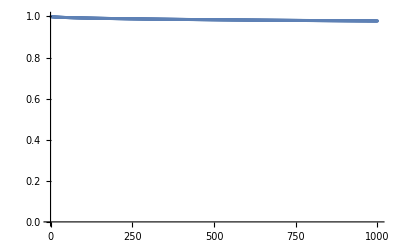

```mathematica
ListPlot[fidelityTable1,PlotRange-> {{0,1000},{0, 1}}]
```

```mathematica
N[Max[fidelityTable1]]
```

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(4209929 (921650572742172/11920928955078125+(219354140616 √(2943135768601/5))/11920928955078125) (153651099728568734448/59604644775390625+(219354140616 √(2943135768601/5))/11920928955078125))/(4350554 (952435678554672/11920928955078125+(219354140616 √(2943135768601/5))/11920928955078125) (148684711478047671948/59604644775390625+(219354140616 √(2943135768601/5))/11920928955078125))+(4209929 (58985636655499008/11920928955078125+(14038664999424 √(2943135768601/5))/11920928955078125) (9833670382628399004672/59604644775390625+(14038664999424 √(2943135768601/5))/11920928955078125))/(4350554 (60955883427499008/11920928955078125+(14038664999424 √(2943135768601/5))/11920928955078125) (9515821534595051004672/59604644775390625+(14038664999424 √(2943135768601/5))/11920928955078125)).

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(4209929 (283576056010301/48828125000000000000+(12629787 √(34962040702393825572101/5))/48828125000000000000) (19666146435292629709569/244140625000000000000+(12629787 √(34962040702393825572101/5))/48828125000000000000))/(4350554 (293048396260301/48828125000000000000+(12629787 √(34962040702393825572101/5))/48828125000000000000) (19030468394331952459569/244140625000000000000+(12629787 √(34962040702393825572101/5))/48828125000000000000))+(4209929 (283576056010301/12207031250000000000+(12629787 √((349620407«5»825572101)/5))/12207031250000000000) (19666146435292629709569/61035156250000000000+(12629787 √(34962040702393825572101/5))/12207031250000000000))/(4350554 (293048396260301/12207031250000000000+(12629787 √((349620407«5»825572101)/5))/12207031250000000000) (19030468394331952459569/61035156250000000000+(12629787 √(34962040702393825572101/5))/12207031250000000000)).

0.999994